```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["input.txt","Lines"];
```

```mathematica
data=ToExpression@data;
```

```mathematica
data//Total
```

595

```mathematica
freq={0};
i=0;
```

```mathematica
run=True;
e=0;
While[run,
e=Last@freq+data⟦Mod[i,Length@data]+1⟧;
If[MemberQ[freq,e],
Print[e]; run=False;,
AppendTo[freq,e];i++];
]
```

80598

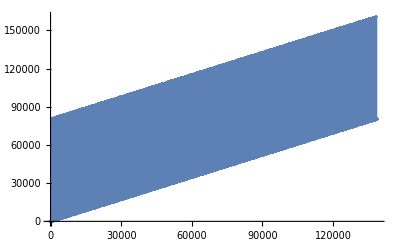

```mathematica
ListLinePlot@freq
```